# Schwinger Effect in de Sitter Space - Conformal Time Coordinates

## Lagrangian:

## For a free particle in de Sitter space, the Lagrangian (in conformal time coordinates) is:

```mathematica
η'[T]D[-1/(λ^2 η[T]),T] (*Product of first terms of each vector*)
```

η'[T]^2/(λ^2 η[T]^2)

```mathematica
x'[T] D[x[T]/(λ η[T])^2,T](*Product of second terms of each vector*)
```

x'[T] (x'[T]/(λ^2 η[T]^2)-(2 x[T] η'[T])/(λ^2 η[T]^3))

```mathematica
FullSimplify[η'[T]D[-1/(λ^2 η[T]),T]+x'[T] D[x[T]/(λ η[T])^2,T]] (* Product of both vectors *)
```

(-2 x[T] x'[T] η'[T]+η[T] (x'[T]^2+η'[T]^2))/(λ^2 η[T]^3)

```mathematica
LC=FullSimplify[m/(2n)((-η'[T]^2)/(λ η[T])^2+x'[T]^2/(λ η[T])^2)-(m n)/2] (* The Lagrangian *)
```

-(m (n^2 λ^2 η[T]^2-x'[T]^2+η'[T]^2))/(2 n λ^2 η[T]^2)

## Find the equations of motion:

```mathematica
xeqc =FullSimplify[D[D[LC,x'[T]],T]-D[LC,x[T]]==0, Assumptions->{m>0,n>0,λ>0}]
```

x''[T]==(2 x'[T] η'[T])/η[T]

```mathematica
teqc=FullSimplify[D[D[LC,η'[T]],T]-D[LC,η[T]]==0, Assumptions->{m>0,n>0,λ>0}]
```

η''[T]==(x'[T]^2+η'[T]^2)/η[T]

## Solve the equation of motion to get x(T) and η(T):

## Attempt at reparametrized solutions:

```mathematica
Clear[solxr,soltr]
```

```mathematica
eta[T_]:=c4/(Cos[c1 T+c2]);
ex[T_]:=c4 Tan[c2+c1 T]+c3;
```

```mathematica
solconst=Solve[{eta[0]==EA,eta[1]==EB,ex[0]==XA,ex[1]==XB},{c1,c2,c3,c4}]/.{C[1]->0,C[2]->0}//Simplify;
```

```mathematica
solINI=Simplify[solconst,XB>XA>0&&EA<EB<0]
```

{{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→-(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]},{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]}}

### Test the solutions by plugging them back into the original equations of motion:

```mathematica
(*Check eom satisfied: should give constants*)
Px=D[ex[T],T]/(H^2 eta[T]^2 ) (*linear momentum in the x-direction along the particle's trajectory*)
En=-(eta[T]D[eta[T],T]-ex[T]D[ex[T],T])/(H^2 eta[T]^2)//Simplify (*(de Sitter) energy along the particle's trajector*)
CQ={Px,En}; (*constants of motion*)
H=1;
dsConstEta= ((Integrate[D[ex[T],T]/(-H eta[T]),T]/.T->1)-(Integrate[D[ex[T],T]/(-H eta[T]),T]/.T->0))//FullSimplify;(*geodesic distance for eta=constant*)
```

c1/c4

(c1 c3)/c4

```mathematica
(*check original eom*)
D[eta[T],{T,2}]-(D[eta[T],T]^2+D[ex[T],T]^2)/eta[T]//Simplify
D[ex[T],{T,2}]-2 D[eta[T],T]D[ex[T],T]/eta[T]
```

0

0

#### Correct solutions!^

## Trajectory plots:

```mathematica
Clear[XA,XB,EA, EB, n,CQ,dsConstEta,solINI,par];
```

```mathematica
(*par={XA->1,XB->4,EA-> 1, EB -> 1,λ->-1,n->1(*,m->1*)};
par2={XA->1,XB->4,EA-> 1, EB -> 1,λ->1,n->1(*,m->1,n->1*)};*)(* Different parameters *)
```

```mathematica
par={EA->-5,EB->-5,XA->1,XB->10};
solINI/.par//N
{Re[ex[T]/.solINI⟦1⟧/.par],Re[eta[T]/.solINI⟦1⟧/.par]}/.T->0.5
{Im[ex[T]/.solINI⟦1⟧/.par],Im[eta[T]/.solINI⟦1⟧/.par]}/.T->0.5
CQ//.solINI⟦1⟧//.par//N
dsConstEta//.solINI⟦1⟧//.par//N
```

{{c3→5.5,c4→2.17945,c1→2.23954,c2→2.02182},{c3→5.5,c4→-2.17945,c1→-2.23954,c2→1.11977}}

{5.5,-2.17945}

{0,0}

{1.02757,5.65164}

2.94444

```mathematica
sol1=Solve[(solINI[[1,2,2]]/.{EA->EB})==0,XB]
```

{{XB→-2 EB+XA},{XB→2 EB+XA}}

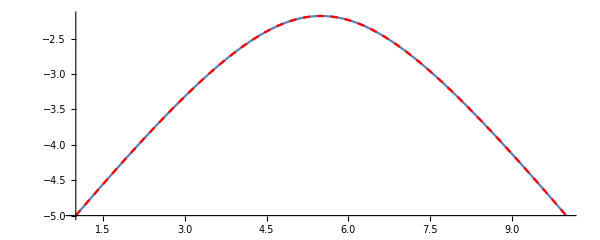

```mathematica
Show[ParametricPlot[{Re[ex[T]/.solINI⟦1⟧/.par],Re[eta[T]/.solINI⟦1⟧/.par]},{T,0,1}],
ParametricPlot[{Re[ex[T]/.solINI⟦2⟧/.par],Re[eta[T]/.solINI⟦2⟧/.par]},{T,0,1},PlotStyle->{Red, Dashed}],ImageSize->600]
```

## Simplified expressions for η:

```mathematica
f=soltr[T]/.par
f2=soltr[T]/.par2
```

-Sinh[1]/(-Sinh[1-T]-Sinh[T])

Sinh[1]/(Sinh[1-T]+Sinh[T])

## Simplified expressions for x:

```mathematica
g=solxr[T]/.par
g2=solxr[T]/.par2
```

(Sinh[1-T]+4 Sinh[T])/(Sinh[1-T]+Sinh[T])

(-Sinh[1-T]-4 Sinh[T])/(-Sinh[1-T]-Sinh[T])

## Plots of x and η wrt to T :

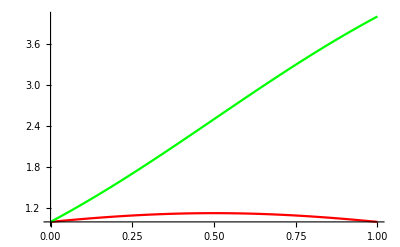

```mathematica
Plot[{f2,g2},{T,0,1},PlotStyle->{Red,Green}]
```

## Trajectory for particle in electric field (η versus x) :

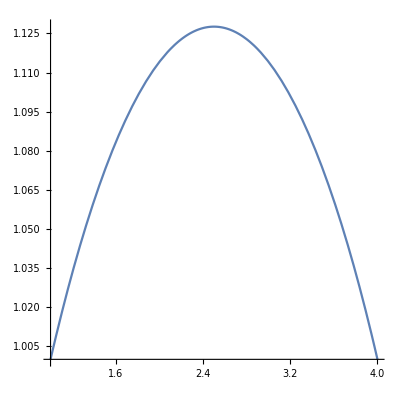

```mathematica
ParametricPlot[{g,f},{T,0,1},AspectRatio->1]
```

## Attempt at Manipulate function:

```mathematica
Clear[xm,tm]
```

```mathematica
(* Variables storing expressions for x and t *)
x
```

(EB XA Sinh[n (-1+T) λ]-EA XB Sinh[n T λ])/(EB Sinh[n (-1+T) λ]-EA Sinh[n T λ])

```mathematica
(*rep={xa->xaa,xb->xbb,ta->taa,tb->tbb,m->mm,n->nn,k->kk};*)
```

```mathematica
eta
```

(EA EB Sinh[n λ])/(-EB Sinh[n (-1+T) λ]+EA Sinh[n T λ])

```mathematica
nnn=n/.Soln[[4]]/.{C[1]->-1} (* General form for the dominant saddle point that we determine later *)
```

(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k

```mathematica
Manipulate[ 
ParametricPlot[{(EB XA Sinh[n (-1+T) λ]-EA XB Sinh[n T λ])/(EB Sinh[n (-1+T) λ]-EA Sinh[n T λ]),(EA EB Sinh[n λ])/(-EB Sinh[n (-1+T) λ]+EA Sinh[n T λ])},{T,0,1},AspectRatio->Full,ImageSize->500,PlotRange->All, AxesLabel->{HoldForm[x[T]],η[T]}]
,
{{XA,0},0,5},
{{XB,5},0,5},
{{EA,1},1,10},
{{EB,1},1,10},
{{λ,1},-5,5},{{n,1},0.1,10}]
```

## Find the classical action:

```mathematica
L=FullSimplify[LC/.repl] (* Storing the Lagrangian with the solution plugged in *)
```

(m n ((XA-XB)^2-EB^2 Cosh[2 n (-1+T) λ]-EA^2 Cosh[2 n T λ]+2 EA EB Cosh[n (-1+2 T) λ]))/(2 (EB Sinh[n (-1+T) λ]-EA Sinh[n T λ])^2)

```mathematica
Scl=FullSimplify[Integrate[L,{T,0,1}]] (* Integrating the Lagrangian over T to get the classical action *)
```

(2 EA EB m (-n λ+Coth[n λ])+m (-EA^2-EB^2+(XA-XB)^2) Csch[n λ])/(2 EA EB λ)

```mathematica
Scl/.{XA->1,EA->1} (* Using simplified initial values for x and η *)
```

(2 EB m (-n λ+Coth[n λ])+m (-1-EB^2+(1-XB)^2) Csch[n λ])/(2 EB λ)

## Evaluate the prefactor

This is not its derivation but just an evaluation where the prefactor is 1/Sqrt(Det[mx]) where the mx is a matrix with entries given below by Scl1, Scl2, Scl3, and Scl4.

```mathematica
Scl1=D[Scl,XA,XB] (* Evaluating each entry in the matrix *)
```

-(m Csch[n λ])/(EA EB λ)

```mathematica
Scl2 = D[Scl,XA,EB]
```

-(m (XA-XB) Csch[n λ])/(EA EB^2 λ)

```mathematica
Scl3 = D[Scl,EA,XB]
```

(m (XA-XB) Csch[n λ])/(EA^2 EB λ)

```mathematica
Scl4 = D[Scl,EA,EB]
```

(m (-n λ+Coth[n λ]))/(EA EB λ)-(2 EB m (-n λ+Coth[n λ])-2 EA m Csch[n λ])/(2 EA EB^2 λ)-(2 EA m (-n λ+Coth[n λ])-2 EB m Csch[n λ])/(2 EA^2 EB λ)+(2 EA EB m (-n λ+Coth[n λ])+m (-EA^2-EB^2+(XA-XB)^2) Csch[n λ])/(2 EA^2 EB^2 λ)

```mathematica
Mx=FullSimplify[({{Scl1, Scl2}, {Scl3, Scl4}})] (* Plugging in all the evaluated entries *)
```

{{-(m Csch[n λ])/(EA EB λ),(m (-XA+XB) Csch[n λ])/(EA EB^2 λ)},{(m (XA-XB) Csch[n λ])/(EA^2 EB λ),(m (EA^2+EB^2+(XA-XB)^2) Csch[n λ])/(2 EA^2 EB^2 λ)}}

```mathematica
Pref=FullSimplify[1/(√Det[Mx])] (* Evaluating and simplifying the full prefactor *)
```

(√2)/(√(-(m^2 (EA^2+EB^2-(XA-XB)^2) Csch[n λ]^2)/(EA^3 EB^3 λ^2)))

## Figure out how to find the kernel!

#### The kernel is ultimately an integral over N from 0 to ∞ of the integrand below (stored as Int):

```mathematica
Int = FullSimplify[Pref*Exp[ⅈ Scl/ℏ]]
```

(√2 ⅇ^(-(ⅈ m (2 EA EB n λ-2 EA EB Coth[n λ]+(EA^2+(EB+XA-XB) (EB-XA+XB)) Csch[n λ]))/(2 EA EB λ ℏ)))/(√(-(m^2 (EA^2+EB^2-(XA-XB)^2) Csch[n λ]^2)/(EA^3 EB^3 λ^2)))

However, this integral is extremely difficult (or impossible?) to solve analytically, so we need to use an approximation.

Specifically, we will use a saddle point approximation. That involves allowing N to be complex, and thus allowing the function (i.e. the integrand) to have dependence on complex N (introducing the complex plane). The original contour of the function in the complex plane is very much oscillatory, with an every increasing amplitude of oscillations, which is why it is so tough to solve the integral analytically. Using Cauchy’s theorem, we can deform the original oscillatory contour of the function, which would be a line integral in the 3D-space and restricted to real values of N, to any other “well-behaved” contour such that the contour does not pass over any undefined points (i.e. the function needs to be holomorphic), and the integral over this new contour would be the same as the original contour integral. To quote Wikipedia:  “...if two different paths connect the same two points, and a function is holomorphic everywhere in between the two paths, then the two path integrals of the function will be the same.” (More about holomorphic functions later?) 

Deforming the original path is helpful in the approximation process since the path can be deformed to pass through the highest stationary point/s, with other conditions satisfied of course, and then the path integral would be dominated by that stationary point (or points). It turns out that the only extrema possible in our case are saddle points, so we deform the path to pass through a saddle point (with steepest descent?). [https://www2.ph.ed.ac.uk/~dmarendu/MOMP/lecture05.pdf]

We have been talking about our oscillatory “function” as the whole integrand, but, ignoring the prefactor for now, truly what is relevant is the classical action, Scl, because when we set (d(Int))/dN=0 in order to find the extrema, we get (d(ⅈScl/ℏ))/dN e^(ⅈScl/ℏ)=0 , where the exponent term can’t go to 0, and ⅈ and ℏ are constants, so we know that the extrema are given by (d(Scl))/dN=0, thus the oscillatory function we are concerned with is just Scl.

## Saddle-point approximation

```mathematica
(* Re[fullinteg/.{xa->0,xb->1,ta->0,tb->1,m->1,k->1,ℏ->1}]//FullSimplify *)
```

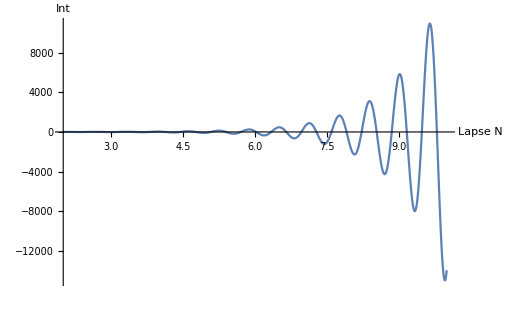

```mathematica
Plot[Re[Int/.{XA->1,XB->2,EA->1,EB->1,m->1,λ-> 1,ℏ->0.1}],{n,2,10},PlotRange->All,AxesLabel->{  HoldForm[N](Lapse), HoldForm[Int]},LabelStyle->{12, GrayLevel[0]}] (* Plot of the function showing oscillatory behavior *)
```

### Find the saddle points:

```mathematica
Soln = Solve[D[Scl, n]==0, n] (* Finding the extrema, where C[1] is a constant integer, so there are infinitely many solutions *)
```

{{n→ConditionalExpression[(-(ⅈ π)/2+2 ⅈ π C[1])/λ,C[1]∈ℤ]},{n→ConditionalExpression[((ⅈ π)/2+2 ⅈ π C[1])/λ,C[1]∈ℤ]},{n→ConditionalExpression[(2 ⅈ π C[1]+Log[(EA^2+EB^2-XA^2+2 XA XB-XB^2+√(-4 EA^2 EB^2+(EA^2+EB^2-XA^2+2 XA XB-XB^2)^2))/(2 EA EB)])/λ,C[1]∈ℤ]},{n→ConditionalExpression[(2 ⅈ π C[1]+Log[-(-EA^2-EB^2+XA^2-2 XA XB+XB^2+√(-4 EA^2 EB^2+(EA^2+EB^2-XA^2+2 XA XB-XB^2)^2))/(2 EA EB)])/λ,C[1]∈ℤ]}}

```mathematica
FullSimplify[n/.Soln[[4]]/.C[1]->1]
```

(2 ⅈ π+Log[-(-EA^2-EB^2+XA^2+√(-4 EA^2 EB^2+(EA^2+EB^2-(XA-XB)^2)^2)-2 XA XB+XB^2)/(2 EA EB)])/λ

```mathematica
FullSimplify[n/.Soln[[3]]/.C[1]->1]
```

(2 ⅈ π+Log[(EA^2+EB^2-XA^2+√(-4 EA^2 EB^2+(EA^2+EB^2-(XA-XB)^2)^2)+2 XA XB-XB^2)/(2 EA EB)])/λ

```mathematica
FullSimplify[FullSimplify[n/.Soln[[4]]/.C[1]->1] ==FullSimplify[n/.Soln[[3]]/.C[1]->1]]//.{XA->0,XB->2,EA->1,EB->1,m->1,λ-> 1,ℏ->0.1}
```

True

#### Solve each conditional expression with given parameters and with different choices of C to check for the different saddle points. All the saddle points lie in two vertical lines equidistant from the imaginary axis on both sides (infinite number of saddle points). It turns out later that the saddle point of our concern is one of the four (the fourth one in the given sequence here) acquired by setting C=-1.

```mathematica
Test = {XA->1,XB->2,EA->1,EB->1,m->1,λ-> 1,ℏ->1,C[1]->0};
```

```mathematica
Sp1 = FullSimplify[n/.Soln⟦1⟧/.Test]
```

-(ⅈ π)/2

```mathematica
Sp2 = FullSimplify[n/.Soln⟦2⟧/.Test]
```

(ⅈ π)/2

```mathematica
Sp3 = FullSimplify[n/.Soln⟦3⟧/.Test ]
```

(ⅈ π)/3

```mathematica
Sp4 = FullSimplify[n/.Soln⟦4⟧/.Test ]
```

-(ⅈ π)/3

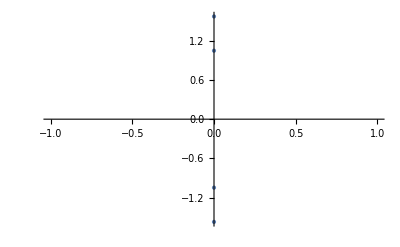

```mathematica
Pl1 = ListPlot[{{Re[Sp1],Im[Sp1]},{Re[Sp2],Im[Sp2]},{Re[Sp3],Im[Sp3]},{Re[Sp4],Im[Sp4]}},PlotStyle->PointSize[Large], PlotRange->All,LabelStyle->{12, GrayLevel[0]}] (* Plot the four saddle points with the given parameters and C=-1 *)
```

```mathematica
Clear[Sp,Sp1,Sp2,Sp3,Sp4,Test,Test1,Pl1,Pl2]
Clear[Pl2]
```

#### Attempt at using Manipulate function to test different saddle points corresponding to different choice of C:

```mathematica
Test1 = {XA->1,XB->2,EA->1,EB->1,m->1,λ-> 1,ℏ->1,C[1]->c1};
```

```mathematica
Sp0 = FullSimplify[ n/.Soln⟦1⟧/.Test1,c1∈Integers && c1∈Reals ]
```

1/2 ⅈ (-1+4 c1) π

```mathematica
Sp11 = FullSimplify[n/.Soln⟦1⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

1/2 ⅈ (-1+4 c1) π

```mathematica
Sp22 = FullSimplify[n/.Soln⟦2⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

1/2 ⅈ (π+4 c1 π)

```mathematica
Sp33 = FullSimplify[n/.Soln⟦3⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

1/3 ⅈ (π+6 c1 π)

```mathematica
Sp44 = FullSimplify[n/.Soln⟦4⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

1/3 ⅈ (-1+6 c1) π

```mathematica
Manipulate[
 ListPlot[{{Re[Sp11]/.c1->cc,Im[Sp11]/.c1->cc},{Re[Sp22]/.c1->cc,Im[Sp22]/.c1->cc},{Re[Sp33]/.c1->cc,Im[Sp33]/.c1->cc},{Re[Sp44]/.c1->cc,Im[Sp44]/.c1->cc}},PlotStyle->PointSize[Large](*, PlotRange->All*)],
{{cc,0},-10,10, 1}
]
```

## Make contour plots of the exponent to put the saddle points in context:

#### Contour plot of the real part of the exponent (Pl2) and the imaginary part of the exponent (Pl3), along with the saddle points (Replot and Implot). As before, we are not yet concerned with the complete function since the exponent suffices in allowing us to make the general approximation:

```mathematica
Pl2 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -6, 6},{ ni, -6, 6}, ColorFunction->"TemperatureMap", Contours->300,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of the real part of the exponent. *)
```

-Graphics-

```mathematica
Replot=Show[Pl2,Pl1] (* Showing with the saddle points *)
```

-Graphics-

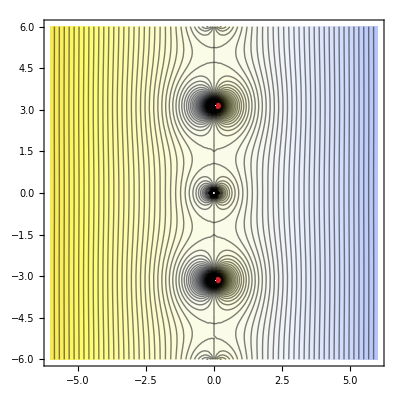

```mathematica
Pl3 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -6, 6},{ ni, -6, 6}, ColorFunction->"TemperatureMap", Contours->100,LabelStyle->{12, GrayLevel[0]}](* Contour plot of the imaginary part of the exponent. *)
```

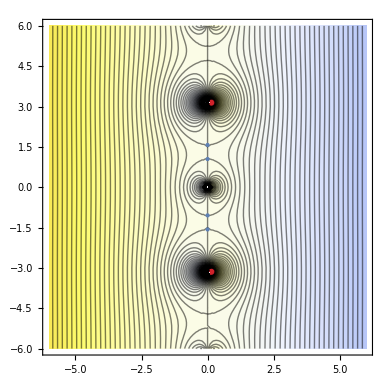

```mathematica
Implot=Show[Pl3,Pl1] (* Showing with the saddle points *)
```

## Find the lines of steepest descent/ascent:

```mathematica
Sp4
```

-(ⅈ π)/3

```mathematica
-(ⅈ π)/3//N
```

0.-1.0472 ⅈ

Make a contour plot of the imaginary part of the exponent for the hopefully-relevant saddle point value of the exponent (Pl4). We are looking for lines of steepest descent/ascent, which have constant imaginary parts, so this allows us to see the lines of steepest descent/ascent that pass through the saddle point/s. Note that n is set to Sp4.

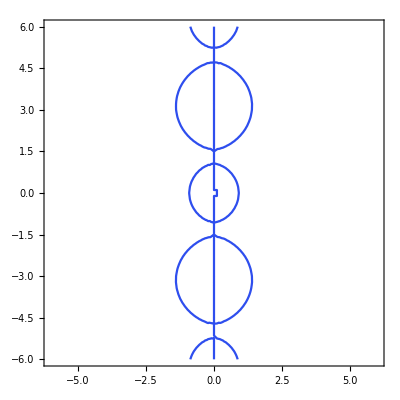

```mathematica
Pl4 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/.Test/.{n->-(ⅈ π)/3}],{nr, -6, 6},{ ni, -6, 6}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of imaginary part of exponent evaluated at fourth saddle point *)
```

```mathematica
Lofda=Show[Pl2,Pl1,Pl4] (* Showing altogether the contour for the real part of the exponent (Pl2), the saddle point (Pl1), and the lines of steepest descent/ascent (Pl4) *)
```

-Graphics-

```mathematica
(*Pl5 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Re[ⅈ Scl/ⅇ^0/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]*)
```

## Determine the relevant saddle point/s:

Now, we add a small perturbation to our seemingly endless line of steepest descent/ascent that stems from Sp4 (why?). Explain this step in greater detail. The perturbation is introduced by giving an imaginary component to ℏ (which is set to 1 for now) in the form of ⅇ^ⅈα where α is the perturbation parameter that can be varied to slightly shift the lines of steepest descent/ascent.

```mathematica
Manipulate[
Show[Pl2,Pl1,ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/ⅇ^(ⅈ α)/.Test/.{n->-(ⅈ π)/3}],{nr, -8, 8},{ ni, -8, 8}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}]],
{{α,-0.01},-0.1,0.1}
] (* This is the same plot as Lofda except with a small perturbation. *)
```

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Pl2,Pl1,].

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Pl2,Pl1,].

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Pl2,Pl1,].

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Pl2,Pl1,].

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Pl2,Pl1,].

Lines of steepest descent and ascent have constant imaginary parts - why?

## Evaluate (or rather, approximate) the integral:

Plugging in the expression for  for n for the dominant saddle point (with C[1]=-1) into the expression that we are integrating gives us an approximation to the integral.

```mathematica
Cond={C[1]->0, EA->1,EB->1,XA-> XB-l,m->1,λ->1,ℏ->1}; (* Redefining xa and xb in terms of l=xb-xa *)
Cond1={C[1]->0, EA->1,EB->1,XA-> XB-l,(*m->1,λ->1,*)ℏ->1};
```

```mathematica
Spfin = FullSimplify[n/.Soln⟦4⟧/.Cond1, Assumptions->l>0] (* General expression for n at the dominant saddle point with given parameters *)
```

Log[1-1/2 l (l+√(-4+l^2))]/λ

```mathematica
FullSimplify[Pref*Exp[ⅈ Scl]/.Cond1 ](* General form of integrand for kernel with given parameters *)
```

(√2 ⅇ^((ⅈ m (-2 n λ+2 Coth[n λ]+(-2+l^2) Csch[n λ]))/(2 λ)))/(√(((-2+l^2) m^2 Csch[n λ]^2)/λ^2))

```mathematica
g=FullSimplify[Exp[ⅈ Scl/ℏ]/.n->Spfin/.Cond1] (* Most general approximation of the integral using saddle point approx. (disregarding prefactor) *)
```

(1-1/2 l (l+√(-4+l^2)))^(-(ⅈ m)/λ)

```mathematica
Abs[g/.Cond1]
```

ⅇ^Im[Log[1-1/2 l (l+√(-4+l^2))]]

For plotting purposes, let' s evaluate g with all parameters defined:

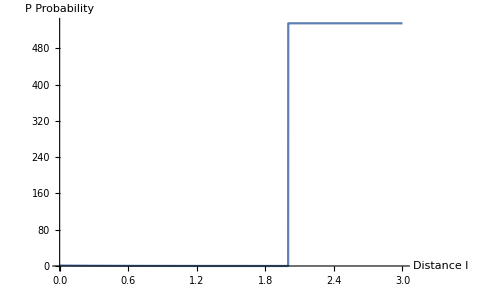

```mathematica
Plot[(Abs[g/.Cond])^2,{l,0,3},PlotRange->All, AxesLabel->{l (Distance), P (Probability)},LabelStyle->{12, GrayLevel[0]}] (* Plot of the probability approximation with respect to l (disregarding prefactor) *)
```

```mathematica
Lcrit=FullSimplify[Reduce[D[(Abs[g])^2, l]==0, {l,λ,m} ]](* Determining the critical distance between the particle and antiparticle (before which they remain virtual particles) *)
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(m Im'[(m Log[1-1/2 l (l+√(-4+l^2))])/λ])/(√(-4+l^2) λ)==0,{l,λ,m}]

```mathematica
IntApprox = FullSimplify[g/.Lcrit⟦2⟧, m ∈Reals && m>0 && k∈ Reals && k>0]  (* Final approximation of kernel with critical distance and other given parameters *)
```

(-(ⅈ (-1+ⅇ^((λ InverseFunction[Im',1,1][0])/m)) √(-1-Cosh[(λ InverseFunction[Im',1,1][0])/m]))/(√2 √(ⅇ^((λ InverseFunction[Im',1,1][0])/m)))+Cosh[(λ InverseFunction[Im',1,1][0])/m])^(-(ⅈ m)/λ)

```mathematica
Prob = IntApprox^2 (* Final approximation of probability with *)
```

ⅇ^(-(m^2 π)/k)

Use n (saddle point) to plot trajectory.

```mathematica
Fcond={l->2m/k,k->1,m->1};
```

```mathematica
Cond1
Fcond
```

```mathematica
{C[1]->-1,ta->0,tb->0,xb->l+xa,ℏ->1}
```

{C[1]→-1,ta→0,tb→0,xb→l+xa,ℏ→1}

```mathematica
nn=FullSimplify[n/.Soln⟦4⟧/.Cond1//.Fcond]
```

-ⅈ π

Lookup de Sitter in Poincare patch (in proper time coordinates and in conformal (time) coordinates)

```mathematica
-dtau^2=ds^2 = -dt^2 + spatial part
= -f(η) dη^2 + spatial part
```

Find derivative of imaginary part of T with respect to internal time, and check which choice of parameters give you negative derivative
ParametricPlot3D for imaginary time, real time, and real x.

```mathematica
Cond2={xa->0,xb->3,ta->0,tb->0,m->1,k->1};
```

```mathematica
ParametricPlot3D[{Re[xm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Im[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Re[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-